/Users/edne8319/Desktop/diff_eq_code_cluster

Here2

{601}

{601,2}

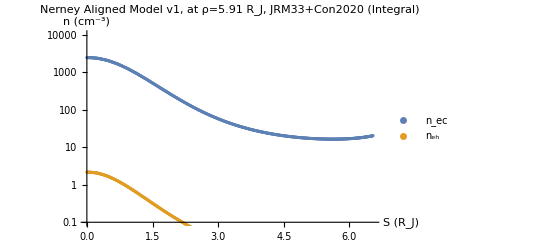

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/diff_eq_code_cluster"]

nec =Flatten[Import["nelec_out_mymodel1_diffeq_jrm33+Con2020_0fillslat-60to60_601_3D_integral_including_feh_only5.91flproperly_aligned_phi0=75.85_perfectaligned_for_4.70-9.71.txt","CSV"],1];

neh =Flatten[Import["neh_out_mymodel1_diffeq_jrm33+Con2020_0fillslat-60to60_601_3D_integral_including_feh_only5.91flproperly_aligned_phi0=75.85_perfectaligned_for_4.70-9.71.txt","CSV"],1];



x =Flatten[Import["x_out_RJ_lat-60to60_1201latvals_only5.91_integralproperly_aligned_phi0=75.85_perfectaligned_for_4.70-9.71.txt","CSV"],1];
y=  Flatten[Import["y_out_RJ_lat-60to60_1201latvals_only5.91_integralproperly_aligned_phi0=75.85_perfectaligned_for_4.70-9.71.txt","CSV"],1];
z =  Flatten[Import["z_out_RJ_lat-60to60_1201latvals_only5.91_integralproperly_aligned_phi0=75.85_perfectaligned_for_4.70-9.71.txt","CSV"],1];


r = Sqrt[x^2+y^2+z^2];
Lat=ArcSin[z/r]; (*Radians*)


(180/Pi)*Lat;


interporder=3;
(*dx=Table[{x[[i,flidx]],1},{i,501,1001,1}];
dy=Table[{y[[i,flidx]],1},{i,501,1001,1}];
dz=Table[{z[[i,flidx]],1},{i,501,1001,1}];
Print["Here1"]*)
d=Table[Sqrt[(x[[i+1]]-x[[i]] )^2+(y[[i+1]]-y[[i]] )^2+(z[[i+1]]-z[[i]] )^2] ,{i,601,1200,1}];

ss=Prepend[Table[Sum[d[[i]],{i,1,j-1}],{j,2,601}],0];
Print["Here2"]
Dimensions[s]
necfl =Table[{ss[[i - 600]],nec[[i]]},{i,601,1201,1}];
Dimensions[necfl]
nehfl =Table[{ss[[i - 600]],neh[[i]]},{i,601,1201,1}];


p1 = ListLogPlot[{necfl,nehfl},AxesLabel->{"S (R_J)","n (cm^-3)"},PlotLabel->"Nerney Aligned Model v1, at ρ=5.91 R_J, JRM33+Con2020 (Integral)",PlotLegends->{"n_ec","n_eh"},PlotRange->{All,{10^-1,10^4}}]



necfl2=Interpolation[necfl];
nehfl2=Interpolation[nehfl];

RJcm = 7.14912*10^9; (*1 Subscript[R, J] = 7.1492*10^4 km = 7.1492*10^7 m = 7.1492*10^9 cm*)
RJcm*Integrate[necfl2[s],{s,ss[[1]],ss[[601]]}]
RJcm*Integrate[nehfl2[s],{s,ss[[1]],ss[[601]]}]
```

```mathematica
s
```

{0,0.0104457,0.0208914,0.0313371,0.0417828,0.0522285,0.0626742,0.0731199,0.0835656,0.0940113,0.104454,0.114906,0.125358,0.13581,0.146261,0.156713,0.167165,0.177617,0.188069,0.198521,0.208973,0.219425,0.229877,0.240328,0.250779,0.261261,0.271743,0.282225,0.292708,0.30319,0.313672,0.324154,0.334636,0.345118,0.3556,0.366083,0.376565,0.387047,0.397529,0.408011,0.418493,0.428976,0.439458,0.44994,0.460422,0.470904,0.481414,0.491967,0.502521,0.513074,0.523627,0.534181,0.544734,0.555287,0.56584,0.576394,0.586947,0.5975,0.608054,0.618607,0.62916,0.639713,0.650267,0.66082,0.671373,0.681927,0.69248,0.70305,0.713703,0.724356,0.735009,0.745663,0.756316,0.766969,0.777622,0.788275,0.798928,0.809581,0.820234,0.830887,0.841541,0.852194,0.862847,0.8735,0.884153,0.894806,0.905459,0.916112,0.92678,0.937554,0.948328,0.959102,0.969876,0.98065,0.991425,1.0022,1.01297,1.02375,1.03452,1.04529,1.05607,1.06684,1.07762,1.08839,1.09917,1.10994,1.12071,1.13149,1.14226,1.15307,1.16398,1.17488,1.18579,1.1967,1.20761,1.21852,1.22943,1.24033,1.25124,1.26215,1.27306,1.28397,1.29487,1.30578,1.31669,1.3276,1.33851,1.34942,1.36032,1.37123,1.38223,1.39328,1.40433,1.41537,1.42642,1.43747,1.44852,1.45957,1.47062,1.48166,1.49271,1.50376,1.51481,1.52586,1.5369,1.54795,1.559,1.57005,1.5811,1.59215,1.60323,1.61442,1.62561,1.63679,1.64798,1.65917,1.67036,1.68154,1.69273,1.70392,1.71511,1.72629,1.73748,1.74867,1.75986,1.77104,1.78223,1.79342,1.80461,1.81579,1.82701,1.83833,1.84965,1.86097,1.87229,1.88361,1.89493,1.90625,1.91757,1.92889,1.94021,1.95154,1.96286,1.97418,1.9855,1.99682,2.00814,2.01946,2.03078,2.0421,2.05346,2.0649,2.07635,2.08779,2.09923,2.11068,2.12212,2.13356,2.14501,2.15645,2.1679,2.17934,2.19078,2.20223,2.21367,2.22511,2.23656,2.248,2.25944,2.27089,2.28242,2.29399,2.30556,2.31713,2.32871,2.34028,2.35185,2.36343,2.375,2.38657,2.39814,2.40972,2.42129,2.43286,2.44444,2.45601,2.46758,2.47916,2.49073,2.5023,2.51387,2.52545,2.53702,2.54859,2.56017,2.57174,2.58331,2.59488,2.60646,2.61809,2.62978,2.64148,2.65318,2.66488,2.67658,2.68827,2.69997,2.71167,2.72337,2.73507,2.74677,2.75846,2.77016,2.78186,2.79356,2.80526,2.81696,2.82865,2.84035,2.85205,2.86375,2.87545,2.88715,2.89884,2.91054,2.92224,2.93394,2.94564,2.95738,2.96916,2.98094,2.99272,3.00449,3.01627,3.02805,3.03983,3.05161,3.06338,3.07516,3.08694,3.09872,3.11049,3.12227,3.13405,3.14583,3.15761,3.16938,3.18116,3.19294,3.20472,3.2165,3.22827,3.24005,3.25183,3.26361,3.27539,3.28716,3.29897,3.31077,3.32258,3.33438,3.34619,3.35799,3.3698,3.38161,3.39341,3.40522,3.41702,3.42883,3.44064,3.45244,3.46425,3.47605,3.48786,3.49966,3.51147,3.52328,3.53508,3.54689,3.55869,3.5705,3.5823,3.59411,3.60592,3.61772,3.6295,3.64127,3.65305,3.66482,3.6766,3.68838,3.70015,3.71193,3.7237,3.73548,3.74726,3.75903,3.77081,3.78258,3.79436,3.80614,3.81791,3.82969,3.84146,3.85324,3.86502,3.87679,3.88857,3.90034,3.91212,3.9239,3.93567,3.94745,3.95922,3.97091,3.98259,3.99428,4.00596,4.01764,4.02932,4.04101,4.05269,4.06437,4.07605,4.08774,4.09942,4.1111,4.12278,4.13447,4.14615,4.15783,4.16951,4.1812,4.19288,4.20456,4.21624,4.22793,4.23961,4.25129,4.26297,4.27465,4.28634,4.29802,4.30954,4.32105,4.33257,4.34409,4.35561,4.36713,4.37864,4.39016,4.40168,4.4132,4.42471,4.43623,4.44775,4.45927,4.47079,4.4823,4.49382,4.50534,4.51686,4.52837,4.53989,4.55141,4.56293,4.57445,4.58596,4.59748,4.609,4.62052,4.63203,4.64337,4.65464,4.66591,4.67719,4.68846,4.69973,4.71101,4.72228,4.73355,4.74483,4.7561,4.76737,4.77865,4.78992,4.80119,4.81247,4.82374,4.83501,4.84629,4.85756,4.86883,4.88011,4.89138,4.90265,4.91393,4.9252,4.93647,4.94774,4.95902,4.97029,4.98129,4.99223,5.00317,5.01411,5.02504,5.03598,5.04692,5.05786,5.0688,5.07973,5.09067,5.10161,5.11255,5.12348,5.13442,5.14536,5.1563,5.16724,5.17817,5.18911,5.20005,5.21099,5.22192,5.23286,5.2438,5.25474,5.26568,5.27661,5.28755,5.29849,5.30943,5.31995,5.33045,5.34095,5.35144,5.36194,5.37244,5.38294,5.39344,5.40393,5.41443,5.42493,5.43543,5.44593,5.45643,5.46692,5.47742,5.48792,5.49842,5.50892,5.51941,5.52991,5.54041,5.55091,5.56141,5.57191,5.5824,5.5929,5.6034,5.6139,5.6244,5.63489,5.64539,5.65544,5.66538,5.67532,5.68526,5.6952,5.70514,5.71509,5.72503,5.73497,5.74491,5.75485,5.76479,5.77473,5.78467,5.79461,5.80455,5.8145,5.82444,5.83438,5.84432,5.85426,5.8642,5.87414,5.88408,5.89402,5.90397,5.91391,5.92385,5.93379,5.94373,5.95367,5.96361,5.97355,5.98349,5.99285,6.00211,6.01137,6.02064,6.0299,6.03916,6.04843,6.05769,6.06695,6.07622,6.08548,6.09474,6.10401,6.11327,6.12253,6.1318,6.14106,6.15032,6.15959,6.16885,6.17811,6.18738,6.19664,6.2059,6.21517,6.22443,6.23369,6.24296,6.25222,6.26148,6.27075,6.28001,6.28927,6.29854,6.3078,6.31706,6.32599,6.33451,6.34303,6.35155,6.36007,6.36859,6.37711,6.38563,6.39415,6.40267,6.41119,6.41971,6.42823,6.43675,6.44527,6.45379,6.46231,6.47083,6.47935,6.48787,6.49639,6.50491,6.51343,6.52195,6.53046,6.53898}

```mathematica
s[[1]]
```

0

```mathematica
s[[601]]
```

6.53898

/Users/edne8319/Desktop/diff_eq_code_cluster

Here2

{683}

{683,2}

Here3

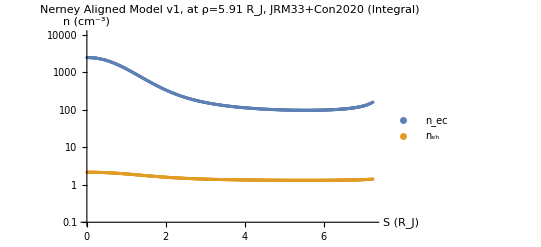

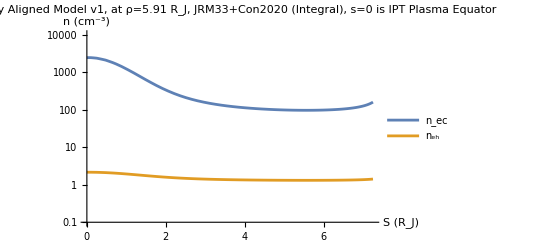

4.76158×10^13

1.57147×10^11

4.15945×10^13

8.27595×10^10

1.14476

1.89884

1.14626

HEREEEEE

1.45758

HEREEEE2

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/diff_eq_code_cluster"]


nec =  Flatten[Import["nelec_out_mymodel1_diffeq_jrm33+Con2020_0fillslat-70to70_601_3D_integral_including_feh_only5.91fl_aligned.txt","CSV"],1];

neh =  Flatten[Import["neh_out_mymodel1_diffeq_jrm33+Con2020_0fillslat-70to70_601_3D_integral_including_feh_only5.91fl_aligned.txt","CSV"],1];

x =  Flatten[Import["x_outlat-70to70_601_3D_integral_only5.91fl_aligned.txt","CSV"],1];
y=  Flatten[Import["y_outlat-70to70_601_3D_integral_only5.91fl_aligned.txt","CSV"],1];
z =Flatten[  Import["z_outlat-70to70_601_3D_integral_only5.91fl_aligned.txt","CSV"],1];


r = Sqrt[x^2+y^2+z^2];
Lat=ArcSin[z/r]; (*Radians*)

(180/Pi)*Lat;
d=Table[Sqrt[(x[[i+1]]-x[[i]] )^2+(y[[i+1]]-y[[i]] )^2+(z[[i+1]]-z[[i]] )^2] ,{i,701,1383,1}];

ss=Prepend[Table[Sum[d[[i]],{i,1,j-1}],{j,2,683}],0];
Print["Here2"]
Dimensions[ss]
necfl =Table[{ss[[i - 700]],nec[[i]]},{i,701,1383,1}];

necflsqrt =Table[{ss[[i - 700]],Sqrt[nec[[i]]]},{i,701,1383,1}];
Dimensions[necfl]
nehfl =Table[{ss[[i - 700]],neh[[i]]},{i,701,1383,1}];

latfl =Table[{ss[[i - 700]],(180/Pi)*Lat[[i]]},{i,701,1383,1}];




Print["Here3"]

p1 = ListLogPlot[{necfl,nehfl},AxesLabel->{"S (R_J)","n (cm^-3)"},PlotLabel->"Nerney Aligned Model v1, at ρ=5.91 R_J, JRM33+Con2020 (Integral)",PlotLegends->{"n_ec","n_eh"},PlotRange->{All,{10^-1,10^4}}]
necfl2sqrt=Interpolation[necflsqrt];
necfl2=Interpolation[necfl];
nehfl2=Interpolation[nehfl];


p2 =LogPlot[{necfl2[s],nehfl2[s]},{s,ss[[1]],ss[[681]]},AxesLabel->{"S (R_J)","n (cm^-3)"},PlotLabel->"Nerney Aligned Model v1, at ρ=5.91 R_J, JRM33+Con2020 (Integral), s=0 is IPT Plasma Equator",PlotLegends->{"n_ec","n_eh"},PlotRange->{All,{10^-1,10^4}}]

RJcm = 7.14912*10^9; (*1 Subscript[R, J] = 7.1492*10^4 km = 7.1492*10^7 m = 7.1492*10^9 cm*)
2*RJcm*Integrate[necfl2[s],{s,ss[[1]],ss[[681]]}]
2*RJcm*Integrate[nehfl2[s],{s,ss[[1]],ss[[681]]}]


2*RJcm*Integrate[necfl2[s],{s,ss[[1]],ss[[302]]}]
2*RJcm*Integrate[nehfl2[s],{s,ss[[1]],ss[[302]]}]

RJcm*Integrate[necfl2[s],{s,ss[[1]],ss[[681]]}]/
(RJcm*Integrate[necfl2[s],{s,ss[[1]],ss[[302]]}])
RJcm*Integrate[nehfl2[s],{s,ss[[1]],ss[[681]]}]/(RJcm*Integrate[nehfl2[s],{s,ss[[1]],ss[[302]]}])


(RJcm*Integrate[necfl2[s],{s,ss[[1]],ss[[681]]}] + RJcm*Integrate[nehfl2[s],{s,ss[[1]],ss[[681]]}])/(RJcm*Integrate[necfl2[s],{s,ss[[1]],ss[[302]]}] +RJcm*Integrate[nehfl2[s],{s,ss[[1]],ss[[302]]}] )

Print["HEREEEEE"]

(RJcm*Integrate[necfl2sqrt[s],{s,ss[[1]],ss[[681]]}] )/(RJcm*Integrate[necfl2sqrt[s],{s,ss[[1]],ss[[302]]}] )

Print["HEREEEE2"]
```

```mathematica
(180/Pi)*Lat[[701]]
(180/Pi)*Lat[[1383]]
```

2.69528×10^-18

68.1924

```mathematica
1383-701
```

682

```mathematica
Dimensions[d]
```

{683}

```mathematica
1001-501
```

500

```mathematica
Dimensions[latfl]
```

{683,2}

```mathematica
latfl[[1,All]]
```

{0,2.69528×10^-18}

```mathematica
latfl[[683,All]]
```

{7.28439,68.1924}

```mathematica
latfl[[302,All]]
```

{3.34363,30.0767}

```mathematica
latfl[[681,All]]
```

{7.24972,67.9999}